```mathematica
gamma0DAB[r_,xi_]:=Exp[-r/xi]
```

```mathematica
gamma0DAB[r,xi]
```

ⅇ^(-r/xi)

```mathematica
Integrate[gamma0DAB[r,xi]*4*Pi*r^2,{r,0,Infinity},Assumptions->xi>0]
```

8 π xi^3

```mathematica
gammaDAB[r_,xi_,eta_]:=Integrate[gamma0DAB[r,xi]*4*Pi*r^2,{r,0,Infinity},Assumptions->xi>0]*gamma0DAB[r,xi]*eta^2
```

```mathematica
IDAB=FullSimplify[Integrate[gammaDAB[r,xi,eta]*Sin[Q*r]/(Q*r)*4*Pi*r^2,{r,0,Infinity}],Assumptions->xi>0&&Q>0]
```

(64 eta^2 π^2 xi^6)/((1+Q^2 xi^2)^2)

```mathematica
GzHF=Integrate[1/(2*Pi)*IDAB*BesselJ[0,Q*z]*Q,{Q,0,Infinity},Assumptions->z>0&&xi>0]
```

Integrate[(IDAB Q BesselJ[0,Q z])/(2 π),{Q,0,∞},Assumptions→z>0&&xi>0]

```mathematica
GzA=Integrate[2*(2*Pi)^2*gammaDAB[r,xi,eta]r/Sqrt[r^2-z^2],{r,z,Infinity}, Assumptions->z>0&&xi>0]
```

64 eta^2 π^3 xi^3 z BesselK[1,z/xi]

```mathematica
Integrate[2*Pi/tl2*((tl2*16 eta^2 π xi^3 z BesselK[1,z/xi])+(tl2*16 eta^2 π xi^3 z BesselK[1,z/xi])^2/2)*BesselJ[0,Q*z]*z,{z,0,Infinity},Assumptions->Q>0&&xi>0]
```

64 eta^2 π^2 xi^6 (1/((1+Q^2 xi^2)^2)+(16 eta^2 π tl2 xi (Q xi (-2+Q^2 xi^2) √(4+Q^2 xi^2)+8 (1+Q^2 xi^2) ArcSinh[(Q xi)/2]))/(Q^3 (4+Q^2 xi^2)^(5/2)))

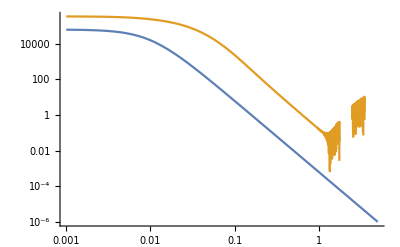

```mathematica
LogLogPlot[{(64 (10^(-5))^2 π^2 100^6)/((1+Q^2 100^2)^2),NIntegrate[2*Pi/22*(Exp[22*16 (10^(-5))^2 π^1 100^3 z BesselK[1,z/100]]-1)*BesselJ[0,Q*z]*z,{z,0,Infinity},Method->"DoubleExponential"]},{Q,0.001,5}]
```